```mathematica
confipot[r_,k_,r0_]:=1/(Exp[(r-r0)/k]+1);
```

Plot::plln: Limiting value rmax in {r,0,rmax} is not a machine-sized real number.

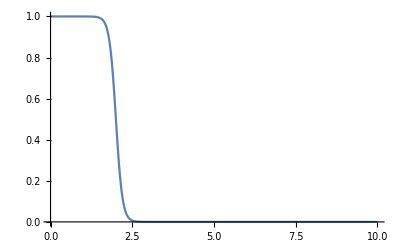

```mathematica
k1=0.1;k2=2 k1;
r01=2;r02=2 r01;
Plot[{confipot[r,k1,r01]},{r,0,rmax}]/.rmax->10
```